```mathematica
xcorrData=Import["~/test.tsv"]
```

{{1.16415×10^-10,0,272,0,-5.82077×10^-11},8190,{1}}
 |  |  |  |

```mathematica
ListLinePlot[xcorrData//Transpose,PlotRange->All]
```

-Graphics-

```mathematica
dataOne=Import["~/WORKSPACE/source1.tsv"]
dataTwo=Import["~/WORKSPACE/source2.tsv"]
```

{{-6.36982×10^-8},{-9.47842×10^-7},47997,{-0.531214}}
 |  |  |  |

{{-0.521316},{-0.508358},47996,{-1.03538},{-1.04747}}
 |  |  |  |

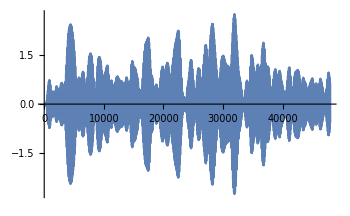

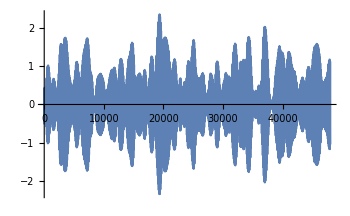

```mathematica
ListLinePlot[dataOne//Flatten]
ListLinePlot[dataTwo//Flatten]
```

```mathematica
Correlation[dataOne//Flatten,dataTwo//Flatten]
```

-0.0971162